```mathematica
(*Вариант 10*)
(*Корнеенко Егор*) 
(*Задание 1*)
 (*n=6*)
f[x_]=(Sinh[√(x^2+x + 5)]+π)/(√(3 x^8+11 x^4+33))
```

(π+Sinh[√(5+x+x^2)])/(√(33+11 x^4+3 x^8))

```mathematica
a=0; b=6; n=6; h=(b-a)/n;
data = N[Table[{a+i*h, f[a+i*h]}, {i,0,n}]](*посчитаем значения функции на отрезке [0,n], разделя отрезок на равные части]*)
```

{{0.,1.35195},{1.,1.48099},{2.,0.540904},{3.,0.236911},{4.,0.173183},{5.,0.173726},{6.,0.212533}}

```mathematica
Buff[x_]=1;
 L[x_]=0;
```

```mathematica
(*строим интерполяционный многочлен Лагранжа*)
sum=0;
For[i=1, i<=n+1, i++,
proizv=1;
Buff[x_]=1;
For[j=1, j<=n+1, j++,
If[
i==j, Continue[];
];
Buff[x_]=Buff[x]*(x-data[[j,1]]);
proizv=proizv*(data[[i,1]]-data[[j,1]]);
];
summand = data[[i,2]]/proizv;
L[x_]=(L[x]+Buff[x]*summand);
]
```

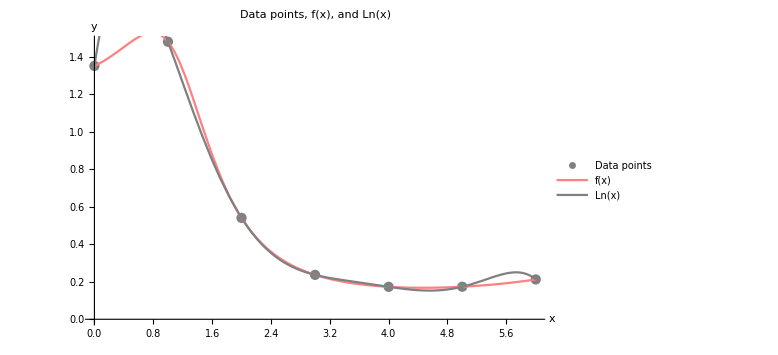

```mathematica
Show[ListPlot[data,PlotStyle->Gray,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Pink,PlotLegends->{"f(x)"}],Plot[L[x],{x,0,n},PlotStyle->Gray,PlotLegends->{"Ln(x)"}],
AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and Ln(x)",ImageSize->Large]
```

```mathematica
Array[dif, {n+1, n+1}, {0,0}];(*создаем массив для конечных разностей*)
```

```mathematica
For[k=1, k<=n, k++,
For[i=n, i>=n-k, i--, dif[i,k]=""](*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
];
```

```mathematica
For[i=0, i<=n,i++,dif[i,0]=data[[i+1,2]]];(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
```

```mathematica
For[k=1, k<=n,k++,(*Считаем конечные разности*)
For[i=0, i<=n-k, i++,
dif[i,k]=dif[i+1, k-1]-dif[i,k-1]
]
];
```

```mathematica
tab=Array[dif, {n+1, n+1},{0,0}];
```

```mathematica
PaddedForm[TableForm[tab], {6,5}] (*получаем таблицу конечных разностей*)
```

1.35195 |  0.12903 | -1.06911 |  1.70520 | -2.10103 |  2.32086 | -2.39069
 1.48099 | -0.94008 |  0.63609 | -0.39582 |  0.21983 | -0.06984 | 
 0.54090 | -0.30399 |  0.24027 | -0.17600 |  0.14999 |  | 
 0.23691 | -0.06373 |  0.06427 | -0.02601 |  |  | 
 0.17318 |  0.00054 |  0.03826 |  |  |  | 
 0.17373 |  0.03881 |  |  |  |  | 
 0.21253 |  |  |  |  |  |

```mathematica
t=(x-a)/h; pn1[x_]=dif[0,0]; p[t_]=1(*строим первый интерполяционный многочлен Ньютона pn1(x)*)
```

1

```mathematica
For[k=1,k<=n, k++,
p[t_]=p[t]*(t-k+1);
pn1[x_]=pn1[x]+dif[0,k]/(k!)*p[t]
]
```

```mathematica
pn1[x]
```

1.35195+0.129032 x-0.534557 (-1+x) x+0.284201 (-2+x) (-1+x) x-0.0875428 (-3+x) (-2+x) (-1+x) x+0.0193405 (-4+x) (-3+x) (-2+x) (-1+x) x-0.00332041 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
pn1[x_]=Simplify[pn1[x]]
```

1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

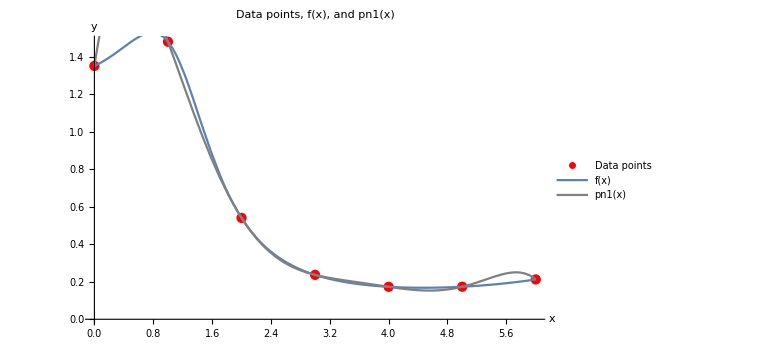

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->pink,PlotLegends->{"f(x)"}],Plot[pn1[x],{x,0,n},PlotStyle->Gray,PlotLegends->{"pn1(x)"}],AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and pn1(x)",ImageSize->Large]
```

```mathematica
Np[x_]=InterpolatingPolynomial[data, x](*строим интерполяционный многочлен Ньютона Np(x) с помощью функции InterpolatingPolynomial*)
```

0.212533+(-6.+x) (-0.189904+(0.0605926+(0.0621898+(-0.0174038+(0.0126996-0.00332041 (-2.+x)) (-5.+x)) (-1.+x)) (-3.+x)) (0.+x))

```mathematica
Np[x_]=Simplify[Np[x]]
```

1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

```mathematica
f[2.4316](*Считаем значения всех фугкций/многочленов в точке 2.4316*)
L[2.4316]
pn1[2.4316]
Np[2.4316]
```

0.350875

0.343952

0.343952

0.343952

```mathematica
R[x_]=Abs[f[x]-Np[x]](*функция погрешности интерполирования многочленом Ньютона*)
```

Abs[-1.35195-2.61987 x+4.22694 x^2-2.23346 x^3+0.563182 x^4-0.0691465 x^5+0.00332041 x^6+(π+Sinh[√(5+x+x^2)])/(√(33+11 x^4+3 x^8))]

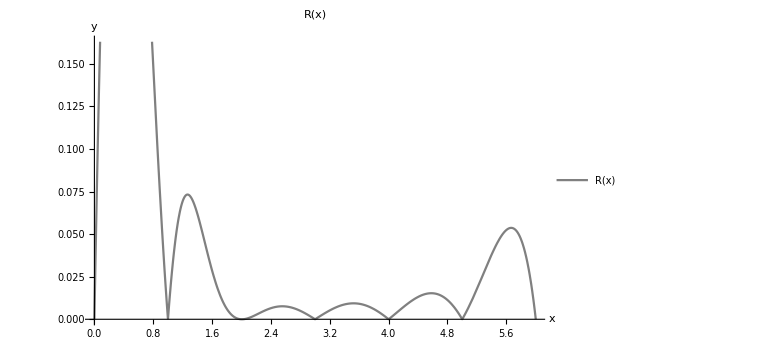

```mathematica
Show[Plot[R[x],{x,0,n}, PlotStyle->Gray, PlotLegends->{"R(x)"}],
AxesLabel->{"x","y"},PlotLabel->"R(x)",ImageSize->Large]
```

```mathematica
(*находим максимум погрешности R(x)на отрезке[0,6]
 с помощью функции найти максимум FindMaximum пакета Mathematica*)
FindMaximum[R[x],{x,0,n}]
```

{0.402046,{x→0.372543}}

```mathematica
(*n=10*)
a=0;b=6;n=10;h=(b-a)/n;
data=N[ Table[{a+i*h,f[a+i*h]},{i,0,n}]]
DataForSplain=data(*сохранил данные для 4 задания*)
```

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}

```mathematica
Buff[x_]=1;
L[x_]=0;
```

```mathematica
(*строим интерполяционный многочлен Лагранжа*)
sum=0;

For[i=1,i≤n+1,i++,proizv=1;
Buff[x_]=1;
For[j=1,j≤n+1,j++,If[i==j, Continue[];];
Buff[x_]=Buff[x]*(x-data⟦j,1⟧);
proizv=proizv*(data⟦i,1⟧-data⟦j,1⟧);];
summand=data⟦i,2⟧/proizv;
L[x_]=(L[x]+Buff[x]*summand);
]
```

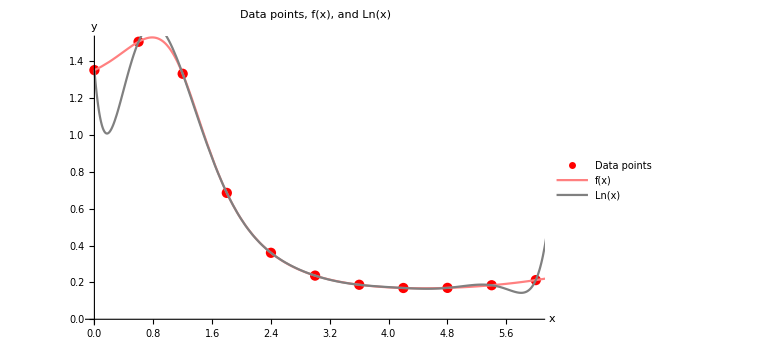

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Pink,PlotLegends->{"f(x)"}],Plot[L[x],{x,0,n},PlotStyle->Gray,PlotLegends->{"Ln(x)"}],
AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and Ln(x)",ImageSize->Large]
```

```mathematica
Clear[dif];
Array[dif,{n+1,n+1},{0,0}];(*создаем массив для конечных разностей*)
```

```mathematica
For[k=1,k≤n,k++,For[i=n,i≥n-k,i--,dif[i,k]=""]
(*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)];
```

```mathematica
For[i=0,i≤n,i++,dif[i,0]=data⟦i+1,2⟧];
(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
```

```mathematica
For[k=1,k≤n,k++,(*Считаем конечные разности*)
For[i=0,i≤n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]
];
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}];
```

```mathematica
PaddedForm[ TableForm[tab],{10,9}] (*получаем таблицу конечных разностей*)
```

1.351954653 |  0.153951267 | -0.327733586 | -0.144944721 |  0.939115725 | -1.853595863 |  2.761333688 | -3.577240138 |  4.244129180 | -4.723086576 |  4.988093894
 1.505905920 | -0.173782319 | -0.472678308 |  0.794171003 | -0.914480138 |  0.907737825 | -0.815906449 |  0.666889042 | -0.478957396 |  0.265007318 | 
 1.332123601 | -0.646460627 |  0.321492696 | -0.120309135 | -0.006742313 |  0.091831376 | -0.149017407 |  0.187931645 | -0.213950078 |  | 
 0.685662975 | -0.324967931 |  0.201183561 | -0.127051447 |  0.085089064 | -0.057186031 |  0.038914238 | -0.026018433 |  |  | 
 0.360695044 | -0.123784370 |  0.074132114 | -0.041962384 |  0.027903032 | -0.018271793 |  0.012895805 |  |  |  | 
 0.236910674 | -0.049652256 |  0.032169730 | -0.014059351 |  0.009631239 | -0.005375988 |  |  |  |  | 
 0.187258418 | -0.017482525 |  0.018110379 | -0.004428113 |  0.004255250 |  |  |  |  |  | 
 0.169775893 |  0.000627854 |  0.013682266 | -0.000172862 |  |  |  |  |  |  | 
 0.170403747 |  0.014310120 |  0.013509404 |  |  |  |  |  |  |  | 
 0.184713867 |  0.027819524 |  |  |  |  |  |  |  |  | 
 0.212533391 |  |  |  |  |  |  |  |  |  |

```mathematica
t=(x-a)/h;pn1[x_]=dif[0,0];
p[t_]=1(*строим первый интерполяционный многочлен Ньютона pn1(x)*)
```

1

```mathematica
For[k=1,k≤n,k++,p[t_]=p[t]*(t-k+1);
pn1[x_]=pn1[x]+dif[0,k]/(k!)*p[t]
]
```

```mathematica
pn1[x_]=Simplify[pn1[x]]
```

1.35195-4.76894 x+21.1867 x^2-34.0133 x^3+27.9651 x^4-13.7075 x^5+4.2577 x^6-0.84853 x^7+0.105364 x^8-0.00742946 x^9+0.000227331 x^10

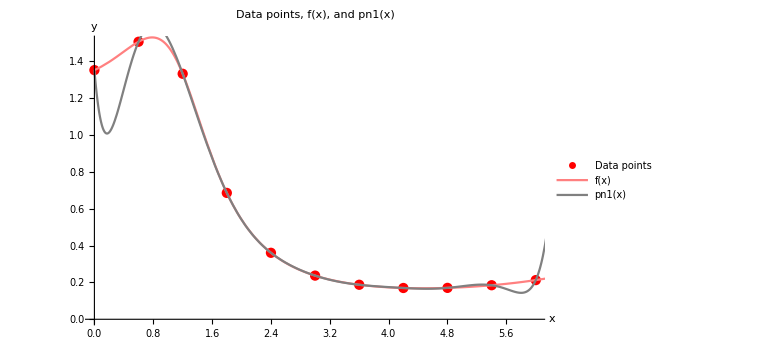

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Pink,PlotLegends->{"f(x)"}],Plot[pn1[x],{x,0,n},PlotStyle->Gray,PlotLegends->{"pn1(x)"}],
AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and pn1(x)",ImageSize->Large]
```

```mathematica
Np[x_]=InterpolatingPolynomial[data,x](*строим интерполяционный многочлен Ньютона Np(x) с помощью функции интерполяционный многочлен InterpolatingPolynomial*)
```

0.212533+(-6.+x) (-0.189904+(0.0605926+(0.0537294+(-0.0170414+(0.00429687+(0.00124703+(-0.00218547+(0.000809347+(-0.000745927+0.000227331 (-1.8+x)) (-4.2+x)) (-2.4+x)) (-0.6+x)) (-5.4+x)) (-4.8+x)) (-1.2+x)) (-3.+x)) (0.+x))

```mathematica
Np[x_]=Simplify[Np[x]]
```

1.35195-4.76894 x+21.1867 x^2-34.0133 x^3+27.9651 x^4-13.7075 x^5+4.2577 x^6-0.84853 x^7+0.105364 x^8-0.00742946 x^9+0.000227331 x^10

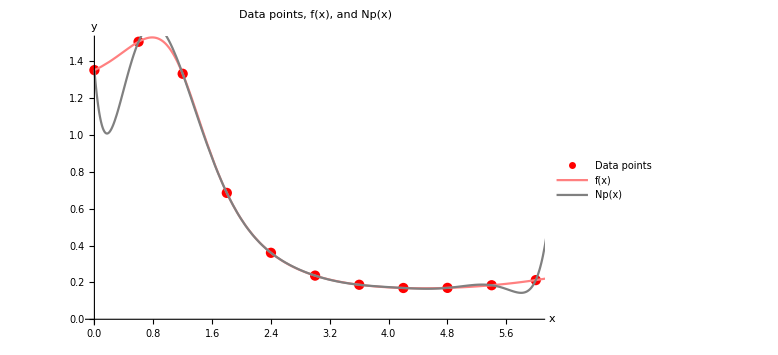

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotLegends->{"Data points"}],Plot[f[x],{x,0,n},PlotStyle->Pink,PlotLegends->{"f(x)"}],Plot[Np[x],{x,0,n},PlotStyle->Gray,PlotLegends->{"Np(x)"}],
AxesLabel->{"x","y"},PlotLabel->"Data points, f(x), and Np(x)",ImageSize->Large]
```

```mathematica
f[2.4316](*Считаем значения всех фугкций/многочленов в точке 2.4316*)
L[2.4316]
pn1[2.4316]
Np[2.4316]
```

0.350875

0.351038

0.351038

0.351038

```mathematica
R[x_]=Abs[f[x]-Np[x]](*функция погрешности интерполирования многочленом Ньютона*)
```

Abs[-1.35195+4.76894 x-21.1867 x^2+34.0133 x^3-27.9651 x^4+13.7075 x^5-4.2577 x^6+0.84853 x^7-0.105364 x^8+0.00742946 x^9-0.000227331 x^10+(π+Sinh[√(5+x+x^2)])/(√(33+11 x^4+3 x^8))]

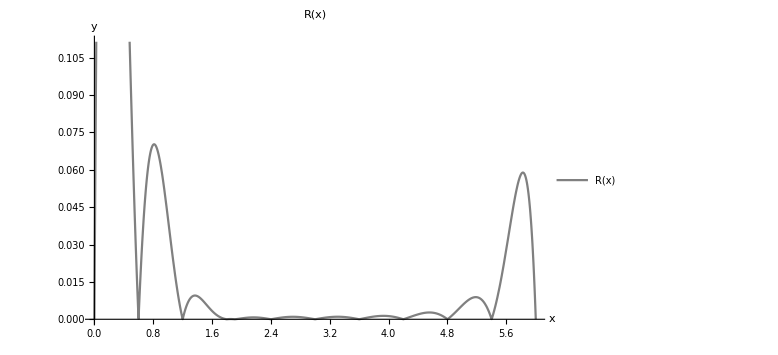

```mathematica
Show[Plot[R[x],{x,0,6}, PlotStyle->Gray, PlotLegends->{"R(x)"}],
AxesLabel->{"x","y"},PlotLabel->"R(x)",ImageSize->Large]
```

```mathematica
(*находим максимум погрешности R(x)на отрезке[0,6] с помощью функции найти максимум FindMaximum пакета Mathematica*)
FindMaximum[R[x],{x,0,6}]
```

{0.383245,{x→0.187988}}

```mathematica
(*ЗАДАНИЕ 2*)
```

```mathematica
n=6
```

6

```mathematica
cheb[x_]=Cos[(π*(2*x+1))/(2*n+2)](*Многочлен Чебышева*)
```

Cos[1/14 π (1+2 x)]

```mathematica
Clear[data]
```

```mathematica
data= N[Table[{(a+b)/2+(b-a)/2*cheb[i], f[(a+b)/2+(b-a)/2*cheb[i]]}, {i,0,n}]]
```

{{5.92478,0.208242},{5.34549,0.182875},{4.30165,0.168805},{3.,0.236911},{1.69835,0.777439},{0.654506,1.5168},{0.0752163,1.36691}}

```mathematica
data=Reverse[data]
```

{{0.0752163,1.36691},{0.654506,1.5168},{1.69835,0.777439},{3.,0.236911},{4.30165,0.168805},{5.34549,0.182875},{5.92478,0.208242}}

```mathematica
Clear[dif]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}](*Создаем массив для разделенных разностей*)
```

{{dif[0,0],dif[0,1],dif[0,2],dif[0,3],dif[0,4],dif[0,5],dif[0,6]},{dif[1,0],dif[1,1],dif[1,2],dif[1,3],dif[1,4],dif[1,5],dif[1,6]},{dif[2,0],dif[2,1],dif[2,2],dif[2,3],dif[2,4],dif[2,5],dif[2,6]},{dif[3,0],dif[3,1],dif[3,2],dif[3,3],dif[3,4],dif[3,5],dif[3,6]},{dif[4,0],dif[4,1],dif[4,2],dif[4,3],dif[4,4],dif[4,5],dif[4,6]},{dif[5,0],dif[5,1],dif[5,2],dif[5,3],dif[5,4],dif[5,5],dif[5,6]},{dif[6,0],dif[6,1],dif[6,2],dif[6,3],dif[6,4],dif[6,5],dif[6,6]}}

```mathematica
For[k=1,k≤n,k++,For[i=n,i≥n-k,i--,dif[i,k]=""]];
(*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
```

```mathematica
For[i=0,i≤n,i++,dif[i,0]=data⟦i+1,2⟧];
(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
```

```mathematica
For [k=1,k≤n,k++,(*Считаем разделенные разности*)
         For [ i=0,i≤n-k,i++,dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(data⟦i+k+1,1⟧-data⟦i+1,1⟧);
]
]
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}]
```

{{1.36691,0.258742,-0.595792,0.246422,-0.0573657,0.00948917,-0.00117389},{1.5168,-0.708307,0.124939,0.0039693,-0.00735518,0.00262241,},{0.777439,-0.415264,0.139416,-0.0305338,0.00646566,,},{0.236911,-0.0523226,0.0280544,-0.00320707,,,},{0.168805,0.0134789,0.0186745,,,,},{0.182875,0.0437901,,,,,},{0.208242,,,,,,}}

```mathematica
PaddedForm[TableForm[tab],{6,5}](*получаем таблицу разделенных разностей*)
```

1.36691 |  0.25874 | -0.59579 |  0.24642 | -0.05737 |  0.00949 | -0.00117
 1.51680 | -0.70831 |  0.12494 |  0.00397 | -0.00736 |  0.00262 | 
 0.77744 | -0.41526 |  0.13942 | -0.03053 |  0.00647 |  | 
 0.23691 | -0.05232 |  0.02805 | -0.00321 |  |  | 
 0.16880 |  0.01348 |  0.01867 |  |  |  | 
 0.18287 |  0.04379 |  |  |  |  | 
 0.20824 |  |  |  |  |  |

```mathematica
Pnr[x_]=tab⟦1,1⟧;
Q[x_]=1;
```

```mathematica
For[i=2,i≤n+1,i++,(*Строим интерполяционный многочлен Ньютона*)Q[x_]=1;
For[k=1,k≤i-1,k++,
Q[x_]=Q[x]*(x-data⟦k,1⟧);
];
Q[x_]=Q[x]*tab⟦1,i⟧;
Pnr[x_]=Pnr[x]+Q[x];];
```

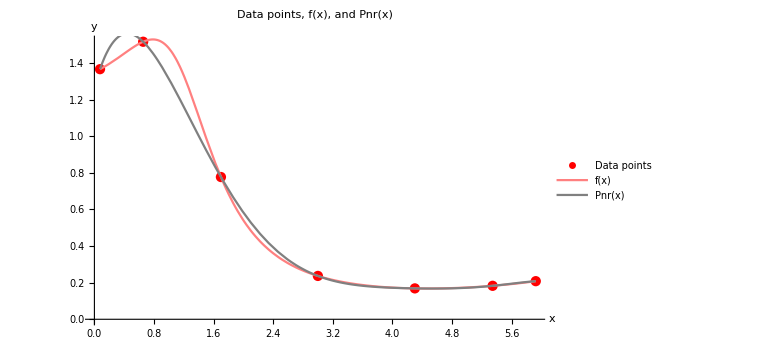

```mathematica
Show[ ListPlot[data, PlotStyle-> Red, PlotLegends->{"Data points"}], Plot[f[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle->Pink, 
PlotLegends->{"f(x)"}], Plot[Pnr[x],{x,Min[data⟦All,1⟧], Max[data⟦All,1⟧]},
 PlotStyle-> Gray,PlotLegends->{"Pnr(x)"}],AxesLabel->{"x","y"}, 
PlotLabel->"Data points, f(x), and Pnr(x)", ImageSize-> Large]
```

```mathematica
Inf=Interpolation[data];
```

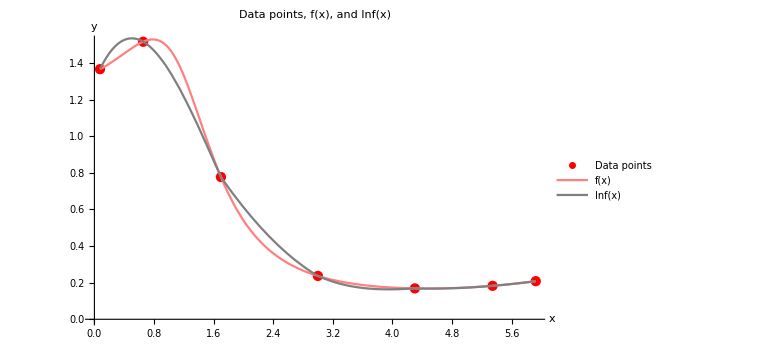

```mathematica
Show[ ListPlot[data, PlotStyle-> Red, PlotLegends->{"Data points"}], Plot[f[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle->Pink, 
PlotLegends->{"f(x)"}], Plot[Inf[x],{x,Min[data⟦All,1⟧], Max[data⟦All,1⟧]},
 PlotStyle-> Gray,PlotLegends->{"Inf(x)"}],AxesLabel->{"x","y"}, 
PlotLabel->"Data points, f(x), and Inf(x)", ImageSize-> Large]
```

```mathematica
(*вычисляем значения функции f (x) и построенных интерполяционных многочленов Pnr(x) и Inf(x)в точке x=2,4316*)f[2.4316]
Pnr[2.4316]
Inf[2.4316]
```

0.350875

0.380613

0.417935

```mathematica
(*находим максимумы абсолютных погрешностей интерполирования функции*)
```

```mathematica
(*находим максимумы абсолютных погрешностей интерполирования функции*)
```

```mathematica
FindMaximum[Abs[f[x]-Pnr[x]],{x,data⟦1,1⟧,data⟦7,1⟧}]
```

{0.113657,{x→0.330325}}

```mathematica
FindMaximum[Abs[f[x]-Inf[x]],{x,data⟦1,1⟧,data⟦7,1⟧}]
```

{0.0779474,{x→0.338156}}

```mathematica
(*n=10*)
n=10
cheb[x_]=Cos[(π*(2*x+1))/(2*n+2)](*Многочлен Чебышева*)
```

10

Cos[1/22 π (1+2 x)]

```mathematica
Clear[data]
```

```mathematica
data= N[Table[{(a+b)/2+(b-a)/2*cheb[i], f[(a+b)/2+(b-a)/2*cheb[i]]}, {i,0,n}]]
data=Reverse[data]
```

{{5.96946,0.210762},{5.7289,0.198185},{5.26725,0.180425},{4.62192,0.168696},{3.8452,0.177356},{3.,0.236911},{2.1548,0.456838},{1.37808,1.13487},{0.732751,1.5271},{0.271104,1.41546},{0.0305357,1.35776}}

{{0.0305357,1.35776},{0.271104,1.41546},{0.732751,1.5271},{1.37808,1.13487},{2.1548,0.456838},{3.,0.236911},{3.8452,0.177356},{4.62192,0.168696},{5.26725,0.180425},{5.7289,0.198185},{5.96946,0.210762}}

```mathematica
Clear[dif]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}](*Создаем массив для разделенных разностей*)
```

{{dif[0,0],dif[0,1],dif[0,2],dif[0,3],dif[0,4],dif[0,5],dif[0,6],dif[0,7],dif[0,8],dif[0,9],dif[0,10]},{dif[1,0],dif[1,1],dif[1,2],dif[1,3],dif[1,4],dif[1,5],dif[1,6],dif[1,7],dif[1,8],dif[1,9],dif[1,10]},{dif[2,0],dif[2,1],dif[2,2],dif[2,3],dif[2,4],dif[2,5],dif[2,6],dif[2,7],dif[2,8],dif[2,9],dif[2,10]},{dif[3,0],dif[3,1],dif[3,2],dif[3,3],dif[3,4],dif[3,5],dif[3,6],dif[3,7],dif[3,8],dif[3,9],dif[3,10]},{dif[4,0],dif[4,1],dif[4,2],dif[4,3],dif[4,4],dif[4,5],dif[4,6],dif[4,7],dif[4,8],dif[4,9],dif[4,10]},{dif[5,0],dif[5,1],dif[5,2],dif[5,3],dif[5,4],dif[5,5],dif[5,6],dif[5,7],dif[5,8],dif[5,9],dif[5,10]},{dif[6,0],dif[6,1],dif[6,2],dif[6,3],dif[6,4],dif[6,5],dif[6,6],dif[6,7],dif[6,8],dif[6,9],dif[6,10]},{dif[7,0],dif[7,1],dif[7,2],dif[7,3],dif[7,4],dif[7,5],dif[7,6],dif[7,7],dif[7,8],dif[7,9],dif[7,10]},{dif[8,0],dif[8,1],dif[8,2],dif[8,3],dif[8,4],dif[8,5],dif[8,6],dif[8,7],dif[8,8],dif[8,9],dif[8,10]},{dif[9,0],dif[9,1],dif[9,2],dif[9,3],dif[9,4],dif[9,5],dif[9,6],dif[9,7],dif[9,8],dif[9,9],dif[9,10]},{dif[10,0],dif[10,1],dif[10,2],dif[10,3],dif[10,4],dif[10,5],dif[10,6],dif[10,7],dif[10,8],dif[10,9],dif[10,10]}}

```mathematica
For[k=1,k≤n,k++,For[i=n,i≥n-k,i--,dif[i,k]=""]];(*Определим элементы массива dif,которые соответствуют пустым клеткам таблицы*)
```

```mathematica
For[i=0,i≤n,i++,dif[i,0]=data⟦i+1,2⟧];
(*заполняем первый столбик таблицы значениями функции в точках с отрезка*)
```

```mathematica
For [k=1,k≤n,k++,(*Считаем разделенные разности*)
         For [ i=0,i≤n-k,i++,dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(data⟦i+k+1,1⟧-data⟦i+1,1⟧);
]
]
```

```mathematica
tab=Array[dif,{n+1,n+1},{0,0}]
```

{{1.35776,0.239853,0.00280749,-0.571652,0.414318,-0.146882,0.0317059,-0.0038276,-0.000143828,0.000232745,-0.0000850628},{1.41546,0.241825,-0.767518,0.308471,-0.0218431,-0.025935,0.0141319,-0.00458079,0.00118243,-0.000272437,},{1.5271,-0.607797,-0.186452,0.248863,-0.114537,0.0355501,-0.00875442,0.0018727,-0.000370011,,},{1.13487,-0.872941,0.377782,-0.107629,0.023723,-0.00414679,0.000601844,-0.0000649449,,,},{0.456838,-0.260208,0.112249,-0.030675,0.00759542,-0.00152827,0.000303657,,,,},{0.236911,-0.0704628,0.0365701,-0.00703466,0.00213323,-0.000369922,,,,,},{0.177356,-0.011149,0.0206208,-0.0012133,0.00103476,,,,,,},{0.168696,0.0181748,0.0183353,0.000984804,,,,,,,},{0.180425,0.0384715,0.0196623,,,,,,,,},{0.198185,0.0522787,,,,,,,,,},{0.210762,,,,,,,,,,}}

```mathematica
PaddedForm[ TableForm[tab],{6,5}](*получаем таблицу разделенных разностей*)
```

1.35776 |  0.23985 |  0.00281 | -0.57165 |  0.41432 | -0.14688 |  0.03171 | -0.00383 | -0.00014 |  0.00023 | -0.00009
 1.41546 |  0.24182 | -0.76752 |  0.30847 | -0.02184 | -0.02594 |  0.01413 | -0.00458 |  0.00118 | -0.00027 | 
 1.52710 | -0.60780 | -0.18645 |  0.24886 | -0.11454 |  0.03555 | -0.00875 |  0.00187 | -0.00037 |  | 
 1.13487 | -0.87294 |  0.37778 | -0.10763 |  0.02372 | -0.00415 |  0.00060 | -0.00006 |  |  | 
 0.45684 | -0.26021 |  0.11225 | -0.03068 |  0.00760 | -0.00153 |  0.00030 |  |  |  | 
 0.23691 | -0.07046 |  0.03657 | -0.00703 |  0.00213 | -0.00037 |  |  |  |  | 
 0.17736 | -0.01115 |  0.02062 | -0.00121 |  0.00103 |  |  |  |  |  | 
 0.16870 |  0.01817 |  0.01834 |  0.00098 |  |  |  |  |  |  | 
 0.18042 |  0.03847 |  0.01966 |  |  |  |  |  |  |  | 
 0.19818 |  0.05228 |  |  |  |  |  |  |  |  | 
 0.21076 |  |  |  |  |  |  |  |  |  |

```mathematica
Pnr[x_]=tab⟦1,1⟧;
Q[x_]=1
```

1

```mathematica
For[i=2,i≤n+1,i++,(*Строим интерполяционный многочлен Ньютона*)Q[x_]=1;
For[k=1,k≤i-1,k++,Q[x_]=Q[x]*(x-data⟦k,1⟧);];
Q[x_]=Q[x]*tab⟦1,i⟧;
Pnr[x_]=Pnr[x]+Q[x];];
```

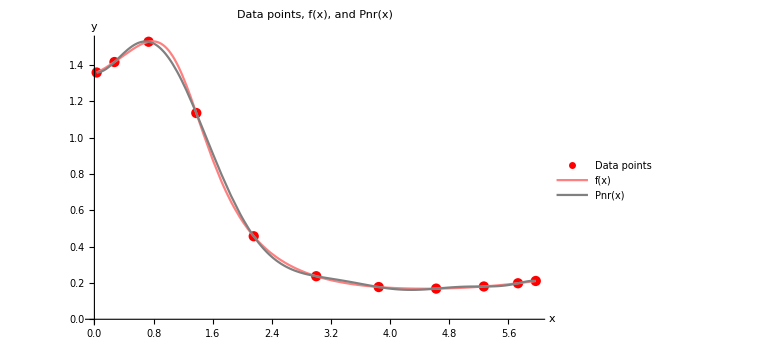

```mathematica
Show[ ListPlot[data, PlotStyle-> Red, PlotLegends->{"Data points"}], Plot[f[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle->Pink, 
PlotLegends->{"f(x)"}], Plot[Pnr[x],{x,Min[data⟦All,1⟧], Max[data⟦All,1⟧]},
 PlotStyle-> Gray,PlotLegends->{"Pnr(x)"}],AxesLabel->{"x","y"}, 
PlotLabel->"Data points, f(x), and Pnr(x)", ImageSize-> Large]
```

```mathematica
Inf=Interpolation[data];
(*интерполирующую функцию Intf (x) n с помощью функции интерполировать Interpolation*)
```

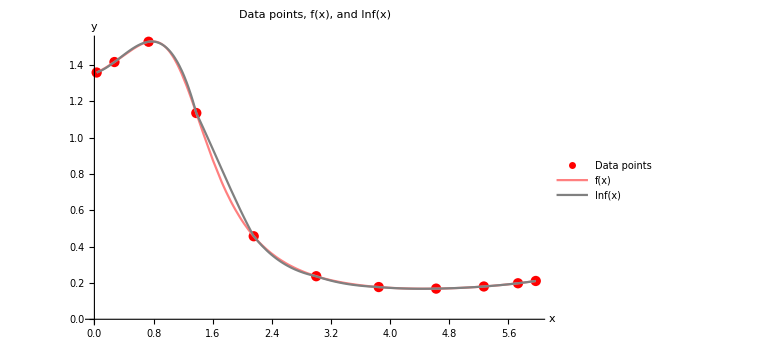

```mathematica
Show[ ListPlot[data, PlotStyle-> Red, PlotLegends->{"Data points"}], Plot[f[x],{x, Min[data⟦ All,1⟧], Max[data⟦ All,1⟧]}, PlotStyle->Pink, 
PlotLegends->{"f(x)"}], Plot[Inf[x],{x,Min[data⟦All,1⟧], Max[data⟦All,1⟧]},
 PlotStyle-> Gray,PlotLegends->{"Inf(x)"}],AxesLabel->{"x","y"}, 
PlotLabel->"Data points, f(x), and Inf(x)", ImageSize-> Large]
```

```mathematica
(*вычисляем значения функции f (x) и построенных интерполяционных многочленов Pnr(x) и Inf(x)в точке x=2,4316*)f[2.4316]
Pnr[2.4316]
Inf[2.4316]
```

0.350875

0.332651

0.343216

```mathematica
(*находим максимумы абсолютных погрешностей интерполирования функции*)
FindMaximum[Abs[f[x]-Pnr[x]],{x,data⟦1,1⟧,data⟦7,1⟧}]
```

{0.00890886,{x→0.134523}}

```mathematica
FindMaximum[Abs[f[x]-Inf[x]],{x,data⟦1,1⟧,data⟦7,1⟧}]
```

{0.00244007,{x→0.13186}}

```mathematica
Rn1[x_]:=Abs[f[x]-Pnr[x]];(*абсолютная погрешность интерполирования многочленом  Ньютона*)
```

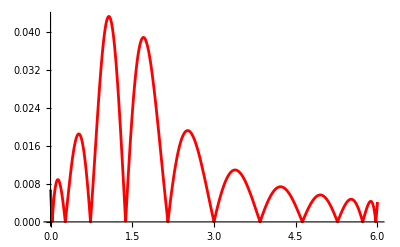

```mathematica
gr1 = Plot[Rn1[x],{x,a,b},PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
Rn2[x_]:=Abs[f[x]-Inf[x]];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

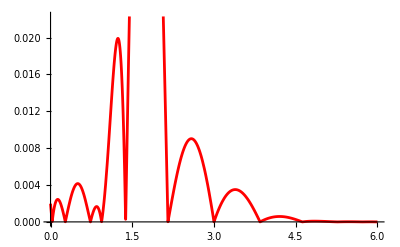

```mathematica
gr2= Plot[Rn2[x],{x,a,b},PlotStyle->{Red,Thickness[0.005]}]
```

```mathematica
(*Задание 3*)
(*На основании решенных нами заданий  и полученных результатов можно сделать заключение о зависимости погрешности интерполирования от числа узлов и их расположения на отрезке.Чем больше узлов мы используем для интерполяции тем точнее будет интерполяционный полиномТакже выбор оптимального распределения узлов (равномерное или неравномерное) может влиять на точность интерполяции.Неравномерно распределенные узлы,такие как узлы Чебышева,могут обеспечить более точное интерполирование в определенных случаях.*)
```

```mathematica
(*Задание 4*)
```

```mathematica
DataForSplain(*таблица значений функции f (x) в равноотстоящих точках отрезка[0,6],полученной в задании 1 при n=10*)
```

{{0.,1.35195},{0.6,1.50591},{1.2,1.33212},{1.8,0.685663},{2.4,0.360695},{3.,0.236911},{3.6,0.187258},{4.2,0.169776},{4.8,0.170404},{5.4,0.184714},{6.,0.212533}}

```mathematica
Sf=Interpolation[DataForSplain, Method->"Spline"];(*интерполяция сплайном Sf (x) с помощью функции интерполировать Interpolation[data,метод Method->“Spline”]*)
```

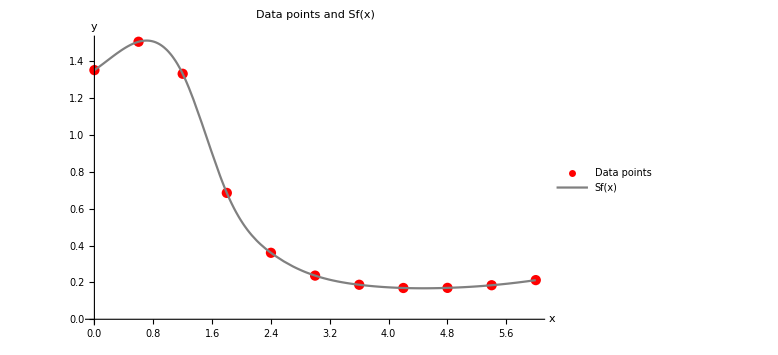

```mathematica
Show[ListPlot[DataForSplain,PlotStyle->Red, PlotLegends->{"Data points"}],Plot[Sf[x],{x,Min[DataForSplain⟦All,1⟧], Max[DataForSplain⟦ All,1⟧]},PlotStyle->Gray,PlotLegends->{"Sf(x)"}], AxesLabel->{"x","y"}, PlotLabel->"Data points and Sf(x)", ImageSize-> Large]
```

```mathematica
(*вычисляем значения функции f (x) и Sf[x] в точке x=2,4316*)
f[2.4316]
Sf[2.4316]
```

0.350875

0.351566